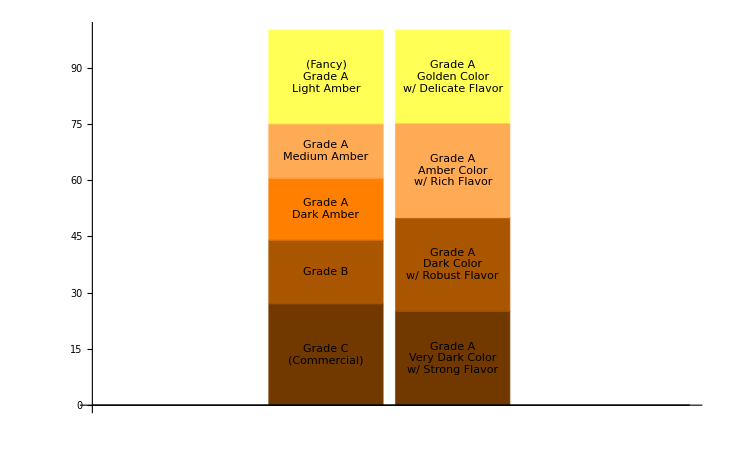

```mathematica
BarChart[
{MapThread[Labeled[#1,#2,Center]&,{Differences@{0,27,44,60.5,75,100},Reverse@{"(Fancy)
Grade A
Light Amber","Grade A
Medium Amber","Grade A
Dark Amber","Grade B","Grade C
(Commercial)"}}],
MapThread[Labeled[#1,#2,Center]&,{Differences@{0,25,50,50,75,100},Reverse@{"Grade A
Golden Color
w/ Delicate Flavor","Grade A
Amber Color
w/ Rich Flavor","","Grade A
Dark Color
w/ Robust Flavor","Grade A
Very Dark Color
w/ Strong Flavor"}}]},
ChartLayout->"Stacked",ChartStyle->{None,{Darker@Darker@Orange,Darker@Orange,Orange,Lighter@Orange,Lighter@Yellow}}]
```